### Initialize constants

Set number of consumers, resources, and enzyme budget

```mathematica
m=5;
p=3;
enzymeBudget=1;
```

Define constants for each consumer

```mathematica
c=enzymeBudget*Normalize[#,Total]&/@RandomReal[{0,1},{m,p}]
```

{{0.48714,0.297146,0.215714},{0.682172,0.0854484,0.232379},{0.140319,0.562714,0.296967},{0.19161,0.439542,0.368848},{0.486611,0.0689441,0.444445}}

```mathematica
g=Table[1,m,p]
```

{{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1}}

```mathematica
z=Table[0.1,m]
```

{0.1,0.1,0.1,0.1,0.1}

Define constants for each resource

```mathematica
κ=Table[1,p]
```

{1,1,1}

```mathematica
μ=Table[0,p]
```

{0,0,0}

### Initialize populations

```mathematica
r0=Table[5,p]
```

{5,5,5}

```mathematica
n0=Table[5,m]
```

{5,5,5,5,5}

### Set up differential equations

find the r’

```mathematica
κ-μ*r-r*Total[n*c]
```

{-0.340915,-1.47486,-0.184221}

```mathematica
n(Total[c*g*r]-z)
```

```mathematica
n*(Total[Transpose[c*g]*r]-z)
```

{0.9,0.9,0.9,0.9,0.9}

```mathematica
Table[n[[a]]*(Sum[c[[a,j]]*g[[a,j]]*r[[j]],{j,1,p}]-z[[a]]),{a,1,m}]
```

{0.9,0.9,0.9,0.9,0.9}

```mathematica
(κ-μ*r[t]-r[t]*Total[n[t]*c])/.{r[t]->r0,n[t]->n0}
```

Thread::tdlen: Objects of unequal length in -1.34091 {1,1,1,1,1} {100,100,100} cannot be combined.

Thread::tdlen: Objects of unequal length in -2.47486 {1,1,1,1,1} {100,100,100} cannot be combined.

Thread::tdlen: Objects of unequal length in -1.18422 {1,1,1,1,1} {100,100,100} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

{1-1.34091 {100,100,100} {1,1,1,1,1},1-2.47486 {100,100,100} {1,1,1,1,1},1-1.18422 {100,100,100} {1,1,1,1,1}}

```mathematica
NDSolve[{
r[0]==r0,
r'[t]==κ-μ*r[t]-r[t]*Total[n[t]*c],
n[0]==n0,
n'[t]==n[t]*(Total[Transpose[c*g]*r[t]]-z)
},
{r,n},
{t,0,10}]
```

Thread::tdlen: Objects of unequal length in {5.,5.,5.,5.,5.} {4.9,4.9,4.9} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve[{r[0]=={5,5,5},r'[t]=={1-1.98785 n[t] r[t],1-1.45379 n[t] r[t],1-1.55835 n[t] r[t]},n[0]=={5,5,5,5,5},n'[t]=={n[t] (-0.1+1. r[t]),n[t] (-0.1+1. r[t]),n[t] (-0.1+1. r[t]),n[t] (-0.1+1. r[t]),n[t] (-0.1+1. r[t])}},{r,n},{t,0,10}]

```mathematica
NDSolve[{
r[0]==r0,
r'[t]==κ-Inactive[Times][μ,r[t]]-Inactive[Times][r[t],Total[Inactive[Times][n[t],c]]],
n[0]==n0,
n'[t]==Inactive[Times][n[t],(Total[Inactive[Times][Transpose[c*g],r[t]]]-z)]
},
{r,n},
{t,0,10}]
```

NDSolve::femcnsd: The PDE coefficient {1-{0,0,0}×r[t]-r[t]×Total[n[t]×{{«3»},{«3»},{«3»},{«3»},{«3»}}]-r'[t],1-{0,0,0}×r[t]-r[t]×Total[n[t]×{{«3»},{«3»},{«3»},{«3»},{«3»}}]-r'[t],1-{0,0,0}×r[t]-r[t]×Total[n[t]×{{«3»},{«3»},{«3»},{«3»},{«3»}}]-r'[t]} does not evaluate to a numeric scalar at the coordinate {5.}; it evaluated to {0.9-0.×Total[0.×{{«3»},{«3»},{«3»},{«3»},{«3»}}]-{0,0,0}×0.,0.9-0.×Total[0.×{{«3»},{«3»},{«3»},{«3»},{«3»}}]-{0,0,0}×0.,0.9-0.×Total[0.×{{«3»},{«3»},{«3»},{«3»},{«3»}}]-{0,0,0}×0.} instead.

```mathematica
NDSolve[{
r[0]==r0,
Splice[Table[Indexed[r'[t],j]==κ[[j]]-μ[[j]]*Indexed[r[t],j]-Indexed[r[t],j]*Sum[Indexed[n[t],a]*c[[a,j]],{a,m}],{j,p}]],
n[0]==n0,
Splice[Table[Indexed[n'[t],a]==Indexed[n[t],a]*(Sum[c[[a,j]]*g[[a,j]]*Indexed[r[t],j],{j,p}]-z[[a]]),{a,m}]]
},
{r,n},
{t,0,10}]
```

NDSolve::overdet: There are fewer dependent variables, {n[t],r[t]}, than equations, so the system is overdetermined.

NDSolve[{r[0]=={100,100,100},r'[t]1==1-(0.48714 n[t]1+0.682172 n[t]2+0.140319 n[t]3+0.19161 n[t]4+0.486611 n[t]5) r[t]1,r'[t]2==1-(0.297146 n[t]1+0.0854484 n[t]2+0.562714 n[t]3+0.439542 n[t]4+0.0689441 n[t]5) r[t]2,r'[t]3==1-(0.215714 n[t]1+0.232379 n[t]2+0.296967 n[t]3+0.368848 n[t]4+0.444445 n[t]5) r[t]3,n[0]=={1,1,1,1,1},n'[t]1==n[t]1 (-0.1+0.48714 r[t]1+0.297146 r[t]2+0.215714 r[t]3),n'[t]2==n[t]2 (-0.1+0.682172 r[t]1+0.0854484 r[t]2+0.232379 r[t]3),n'[t]3==n[t]3 (-0.1+0.140319 r[t]1+0.562714 r[t]2+0.296967 r[t]3),n'[t]4==n[t]4 (-0.1+0.19161 r[t]1+0.439542 r[t]2+0.368848 r[t]3),n'[t]5==n[t]5 (-0.1+0.486611 r[t]1+0.0689441 r[t]2+0.444445 r[t]3)},{r,n},{t,0,10}]

### Test

```mathematica
c=Table[Indexed[cS,{i,j}],{i,m},{j,p}]
```

{{cS11,cS12,cS13},{cS21,cS22,cS23},{cS31,cS32,cS33},{cS41,cS42,cS43},{cS51,cS52,cS53}}

```mathematica
g=Table[Indexed[gS,{i,j}],{i,m},{j,p}]
```

{{gS11,gS12,gS13},{gS21,gS22,gS23},{gS31,gS32,gS33},{gS41,gS42,gS43},{gS51,gS52,gS53}}

```mathematica
z=Table[Indexed[zS,i],{i,m}]
```

{zS1,zS2,zS3,zS4,zS5}

Define constants for each resource

```mathematica
κ=Table[Indexed[κS,i],{i,p}]
```

{κS1,κS2,κS3}

```mathematica
μ=Table[Indexed[μS,i],{i,p}]
```

{μS1,μS2,μS3}

### Initialize populations

```mathematica
r0=Table[Indexed[r0S,i],{i,p}]
```

{r0S1,r0S2,r0S3}

```mathematica
n0=Table[Indexed[n0S,i],{i,m}]
```

{n0S1,n0S2,n0S3,n0S4,n0S5}

```mathematica
{
r[0]==r0,
Splice[Table[Indexed[r'[t],j]==κ[[j]]-μ[[j]]*Indexed[r[t],j]-Indexed[r[t],j]*Sum[Indexed[n[t],a]*c[[a,j]],{a,m}],{j,p}]],
n[0]==n0,
Splice[Table[Indexed[n'[t],a]==Indexed[n[t],a]*(Sum[c[[a,j]]*g[[a,j]]*Indexed[r[t],j],{j,p}]-z[[a]]),{a,m}]]
}
```

{r[0]=={r0S1,r0S2,r0S3},r'[t]1==κS1-μS1 r[t]1-(cS11 n[t]1+cS21 n[t]2+cS31 n[t]3+cS41 n[t]4+cS51 n[t]5) r[t]1,r'[t]2==κS2-μS2 r[t]2-(cS12 n[t]1+cS22 n[t]2+cS32 n[t]3+cS42 n[t]4+cS52 n[t]5) r[t]2,r'[t]3==κS3-μS3 r[t]3-(cS13 n[t]1+cS23 n[t]2+cS33 n[t]3+cS43 n[t]4+cS53 n[t]5) r[t]3,n[0]=={n0S1,n0S2,n0S3,n0S4,n0S5},n'[t]1==n[t]1 (-zS1+cS11 gS11 r[t]1+cS12 gS12 r[t]2+cS13 gS13 r[t]3),n'[t]2==n[t]2 (-zS2+cS21 gS21 r[t]1+cS22 gS22 r[t]2+cS23 gS23 r[t]3),n'[t]3==n[t]3 (-zS3+cS31 gS31 r[t]1+cS32 gS32 r[t]2+cS33 gS33 r[t]3),n'[t]4==n[t]4 (-zS4+cS41 gS41 r[t]1+cS42 gS42 r[t]2+cS43 gS43 r[t]3),n'[t]5==n[t]5 (-zS5+cS51 gS51 r[t]1+cS52 gS52 r[t]2+cS53 gS53 r[t]3)}

```mathematica
DSolve[{
r[0]==r0,
Splice[Table[Indexed[r'[t],j]==κ[[j]]-μ[[j]]*Indexed[r[t],j]-Indexed[r[t],j]*Sum[Indexed[n[t],a]*c[[a,j]],{a,m}],{j,p}]],
n[0]==n0,
Splice[Table[Indexed[n'[t],a]==Indexed[n[t],a]*(Sum[c[[a,j]]*g[[a,j]]*Indexed[r[t],j],{j,p}]-z[[a]]),{a,m}]]
},
{r,n},
{t,0,10}]
```

DSolve::overdet: There are fewer dependent variables than equations, so the system is overdetermined.

DSolve[{r[0]=={r0S1,r0S2,r0S3},r'[t]1==κS1-μS1 r[t]1-(cS11 n[t]1+cS21 n[t]2+cS31 n[t]3+cS41 n[t]4+cS51 n[t]5) r[t]1,r'[t]2==κS2-μS2 r[t]2-(cS12 n[t]1+cS22 n[t]2+cS32 n[t]3+cS42 n[t]4+cS52 n[t]5) r[t]2,r'[t]3==κS3-μS3 r[t]3-(cS13 n[t]1+cS23 n[t]2+cS33 n[t]3+cS43 n[t]4+cS53 n[t]5) r[t]3,n[0]=={n0S1,n0S2,n0S3,n0S4,n0S5},n'[t]1==n[t]1 (-zS1+cS11 gS11 r[t]1+cS12 gS12 r[t]2+cS13 gS13 r[t]3),n'[t]2==n[t]2 (-zS2+cS21 gS21 r[t]1+cS22 gS22 r[t]2+cS23 gS23 r[t]3),n'[t]3==n[t]3 (-zS3+cS31 gS31 r[t]1+cS32 gS32 r[t]2+cS33 gS33 r[t]3),n'[t]4==n[t]4 (-zS4+cS41 gS41 r[t]1+cS42 gS42 r[t]2+cS43 gS43 r[t]3),n'[t]5==n[t]5 (-zS5+cS51 gS51 r[t]1+cS52 gS52 r[t]2+cS53 gS53 r[t]3)},{r,n},{t,0,10}]

```mathematica
sols=NDSolve[{
Splice[Table[ToExpression["r"<>ToString[j]][0]==r0[[j]],{j,p}]],
Splice[Table[ToExpression["r"<>ToString[j]]'[t]==κ[[j]]-μ[[j]]*ToExpression["r"<>ToString[j]][t]-ToExpression["r"<>ToString[j]][t]*Sum[ToExpression["n"<>ToString[a]][t]*c[[a,j]],{a,m}],{j,p}]],
Splice[Table[ToExpression["n"<>ToString[a]][0]==n0[[a]],{a,m}]],
Splice[Table[ToExpression["n"<>ToString[a]]'[t]==ToExpression["n"<>ToString[a]][t]*(Sum[c[[a,j]]*g[[a,j]]*ToExpression["r"<>ToString[j]][t],{j,p}]-z[[a]]),{a,m}]]
},
Join[Table[ToExpression["n"<>ToString[a]],{a,m}],Table[ToExpression["r"<>ToString[j]],{j,p}]],
{t,0,10000}][[1]]
```

{n1→InterpolatingFunction[…],n2→InterpolatingFunction[…],n3→InterpolatingFunction[…],n4→InterpolatingFunction[…],n5→InterpolatingFunction[…],r1→InterpolatingFunction[…],r2→InterpolatingFunction[…],r3→InterpolatingFunction[…]}

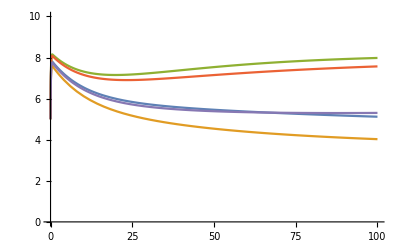

```mathematica
Plot[Evaluate[Through[({n1,n2,n3,n4,n5}/.sols)[t]]],{t,0,100},PlotRange->{All,{0,10}}]
```